# Hands - on start to wolfram Mathematica

## Second Edition

## By Cliff Hastings, Kelvin Mischo and Micheal Morrison

## Jana Rasras June 2023

## chapter 1| Introduction

```mathematica
711/3
```

237

```mathematica
718/3
```

718/3

```mathematica
N[718/3,5] (*Approx answer to 718 divided by 3 rounded to 5 digits*)
```

```mathematica
239.3333333333333333333`5.
```

WolframAlphaQueryParseResults

718/3

```mathematica
a = 5 (* assign a value to a name*)
```

5

```mathematica
3a+1
```

16

```mathematica
Clear[a] (*clear the varible defention of a, which will make a undefined*)
```

```mathematica
Expand[(a+5)(a+9)] (*Expand the algebric experssion*)
```

45+14 a+a^2

```mathematica
Solve[2x - 7 ==0]
```

{{x→7/2}}

WolframAlphaQueryResults

x==7/2

```mathematica
Solve[{2x-7==0, 3x-2y==0},{x,y}]
```

{{x→7/2,y→21/4}}

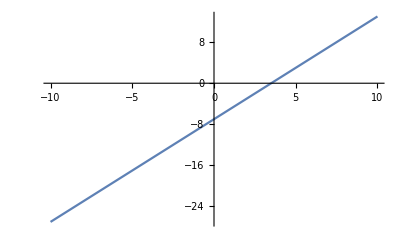

```mathematica
Plot[2x-7, {x,-10,10}] (* plOT the equation, where x goes from -10 to 10*)
```

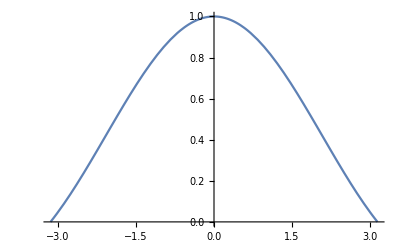

```mathematica
Plot[Sin[x]/x,{x, -Pi, Pi}]
```

WolframAlphaQueryParseResults

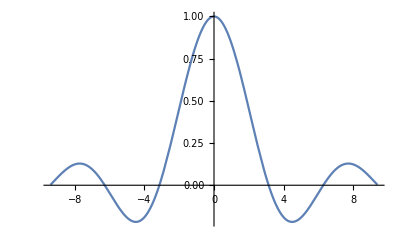

```mathematica
Plot3D[ Sin[x*y], {x,-3,3}, {y, -5, 5}]
```

-Graphics3D-

```mathematica
Table[i^2, {i, 1, 5}]
```

{1,4,9,16,25}

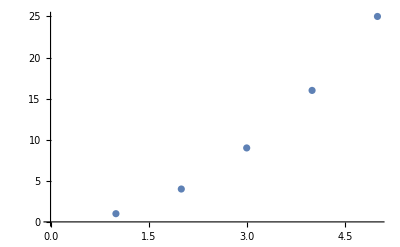

```mathematica
ListPlot[ Table[i^2, {i,1,5}]]
```

```mathematica
Integrate[Sin[x],x] (*Integrate with respect to x*)
```

-Cos[x]

```mathematica
mat1 = {{1,2,3},{3,5,7},{4,6,8}};
```

```mathematica
Det[{{1,2,3},{3,5,7},{4,6,8}}]
```

0

```mathematica
Clear[mat1]
```

## Chapter 2| A sample Project in Mathematica

78.9 yr

```mathematica
data = DeleteCases[Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData[All]}],{_, _Missing}]; (*dELETE missing values*)
```

```mathematica
Short[data]
```

{{Afghanistan,53.25 yr},{Albania,79.23 yr},{Algeria,77.79 yr},{American Samoa,75.06 yr},{Andorra,83.23 yr},{Angola,61.71 yr},{Anguilla,82 yr},{Antigua and Barbuda,77.55 yr},{Argentina,78.07 yr},{Armenia,75.86 yr},{Aruba,77.76 yr},{Australia,82.89 yr},{Austria,82.07 yr},{Azerbaijan,73.88 yr},{Bahamas,75.87 yr},{Bahrain,79.67 yr},{Bangladesh,74.43 yr},{Barbados,78.31 yr},{Belarus,74.01 yr},{Belgium,81.65 yr},{Belize,75.56 yr},{Benin,61.82 yr},{Bermuda,81.83 yr},{Bhutan,71.5 yr},{Bolivia,70.7 yr},{Bosnia and Herzegovina,77.74 yr},{Botswana,65.24 yr},{Brazil,74.98 yr},{British Virgin Islands,79.44 yr},{Brunei,78.14 yr},{Bulgaria,75.3 yr},«173»,{Syria,74.01 yr},{Taiwan,80.95 yr},{Tajikistan,69.06 yr},{Tanzania,69.9 yr},{Thailand,77.41 yr},{Togo,70.99 yr},{Tonga,77.29 yr},{Trinidad and Tobago,74.92 yr},{Tunisia,76.57 yr},{Turkey,75.96 yr},{Turkmenistan,71.54 yr},{Turks and Caicos Islands,80.6 yr},{Tuvalu,68.07 yr},{Uganda,68.58 yr},{Ukraine,73.18 yr},{United Arab Emirates,79.37 yr},{United Kingdom,81.3 yr},{United States,80.43 yr},{United States Virgin Islands,80.05 yr},{Uruguay,78.19 yr},{Uzbekistan,75.03 yr},{Vanuatu,74.87 yr},{Venezuela,72.22 yr},{Vietnam,75.25 yr},{Wallis and Futuna Islands,80.45 yr},{West Bank,76.12 yr},{Western Sahara,63.8 yr},{Yemen,67.18 yr},{Zambia,65.92 yr},{Zimbabwe,62.83 yr}}

```mathematica
Short[SortBy[data,Last]] (*sort from least to greatest*) (*Short  represent only the results*)
```

{{Afghanistan,53.25 yr},{Central African Republic,55.07 yr},{Somalia,55.32 yr},{Mozambique,56.49 yr},{South Sudan,58.6 yr},{Chad,58.73 yr},{Lesotho,58.9 yr},{Eswatini,59.13 yr},{Niger,59.7 yr},{Sierra Leone,60.19 yr},{Nigeria,60.87 yr},{Democratic Republic of the Congo,61.43 yr},{Republic of the Congo,61.69 yr},{Angola,61.71 yr},{Ivory Coast,61.8 yr},{Benin,61.82 yr},{Mali,62.01 yr},{Cameroon,62.79 yr},{Zimbabwe,62.83 yr},{Burkina Faso,63.06 yr},{Guinea-Bissau,63.26 yr},{Guinea,63.53 yr},{Western Sahara,63.8 yr},{Senegal,63.83 yr},{Mauritania,64.86 yr},{Djibouti,65 yr},{South Africa,65.04 yr},{Liberia,65.1 yr},{Botswana,65.24 yr},{Rwanda,65.48 yr},{Haiti,65.61 yr},«173»,{Bermuda,81.83 yr},{Cayman Islands,81.84 yr},{Isle of Man,81.84 yr},{Netherlands,81.95 yr},{Anguilla,82 yr},{Austria,82.07 yr},{Spain,82.21 yr},{New Zealand,82.33 yr},{Norway,82.35 yr},{Liechtenstein,82.36 yr},{France,82.39 yr},{Jersey,82.43 yr},{Sweden,82.6 yr},{Italy,82.67 yr},{Luxembourg,82.78 yr},{South Korea,82.78 yr},{Australia,82.89 yr},{Malta,83 yr},{Guernsey,83.03 yr},{Switzerland,83.03 yr},{Israel,83.15 yr},{Andorra,83.23 yr},{Hong Kong,83.41 yr},{Iceland,83.45 yr},{Canada,83.62 yr},{San Marino,83.68 yr},{Japan,84.65 yr},{Macau,84.81 yr},{Singapore,86.19 yr},{Monaco,89.4 yr}}

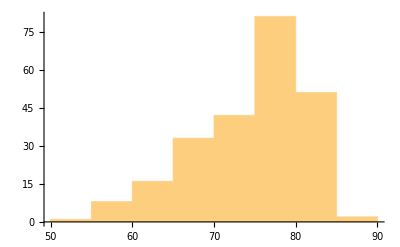

```mathematica
Histogram[data⟦All, 2⟧ ]  (* ESC [[ ESC*)
```

```mathematica
dataAfrica = DeleteCases[Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["Africa"]}],{_, _Missing}];
```

```mathematica
Mean[dataAfrica⟦All,2⟧]
```

66.4587 yr

```mathematica
dataAsia = DeleteCases[Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["Asia"]}],{_, _Missing}];
```

```mathematica
Mean[dataAsia⟦All,2⟧]
```

74.8257 yr

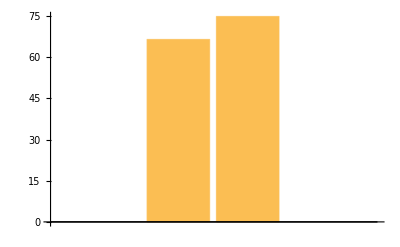

```mathematica
BarChart[{Mean[dataAfrica⟦All,2⟧],Mean[dataAsia⟦All,2⟧]}]
```

```mathematica
dataSouthAmerica= DeleteCases[Table[{i, CountryData[i, "LifeExpectancy"]},{i, CountryData["SouthAmerica"]}],{_, _Missing}];
```

```mathematica
Take[dataSouthAmerica,3]
```

{{Argentina,78.07 yr},{Bolivia,70.7 yr},{Brazil,74.98 yr}}

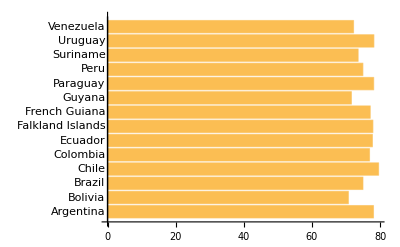

```mathematica
BarChart[dataSouthAmerica⟦All,2⟧, ChartLabels->dataSouthAmerica⟦All,1⟧, BarOrigin->Left]
```

```mathematica
data = Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"GDP"]},CountryData[i,"Name"]],{i, CountryData[]}];
```

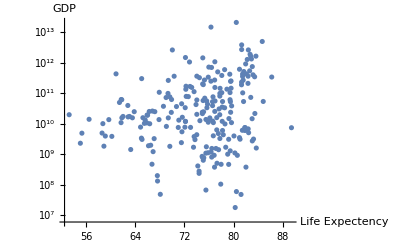

```mathematica
ListLogPlot[data, AxesLabel->{"Life Expectency", "GDP"}]
```

```mathematica
data = Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"InfantMortalityFraction"]},CountryData[i,"Name"]],{i, CountryData[]}];
```

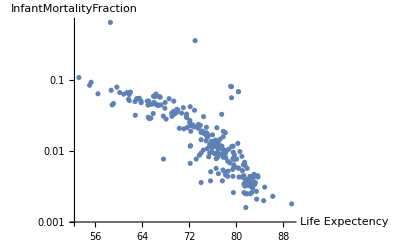

```mathematica
ListLogPlot[data, AxesLabel->{"Life Expectency", "InfantMortalityFraction"}]
```

```mathematica
Manipulate[
plotFn[Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,prop]},
CountryData[i,"Name"]],{i,CountryData[All]}], AxesLabel->{"Life Expetency"," prop"}],{prop,{"InfantMortalityFraction", "GDP", "LiteracyFraction"}}, {{PlotFn, ListLogPlot},{ListPlot, ListLogPlot, ListLogLogPlot}}, SaveDefinitions->True]
```

```mathematica
Clear[data]
```

## Chapter3| Input and Output

```mathematica
2^100
```

1267650600228229401496703205376

WolframAlphaQueryParseResults

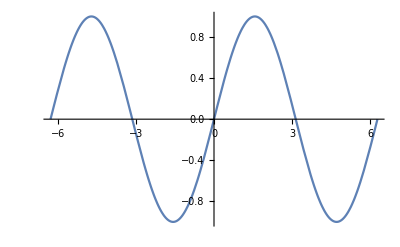

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryParseResults

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]



```mathematica
Plot[Sin[x],{x,0,2 π}]  (* Plot[function, {var, min, max}] *)
```

```mathematica
Expand[(a+b)^10]
```

a^10+10 a^9 b+45 a^8 b^2+120 a^7 b^3+210 a^6 b^4+252 a^5 b^5+210 a^4 b^6+120 a^3 b^7+45 a^2 b^8+10 a b^9+b^10

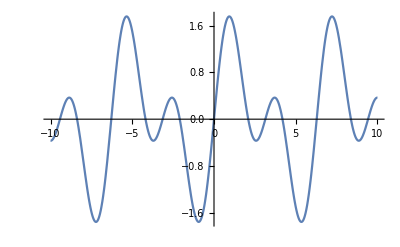

```mathematica
Plot[Sin[x]+ Sin[2x],{x,-10,10}]
```

```mathematica
Solve[-10 +  x^2 ==0,x]
```

{{x→-√10},{x→√10}}

WolframAlphaQueryResults

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Prime[Range[1,25]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

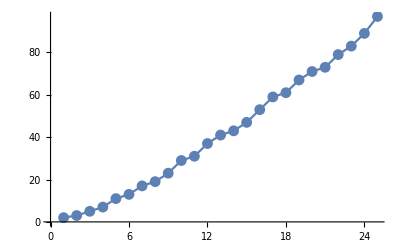

```mathematica
ListLinePlot[Prime[Range[1,25]],Mesh->All]
```

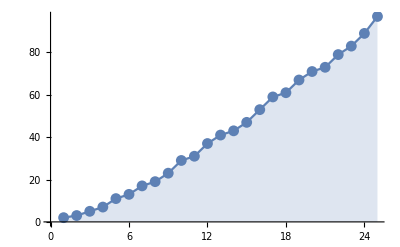

```mathematica
ListLinePlot[Prime[Range[1,25]],Filling-> Automatic, Mesh->All]
```

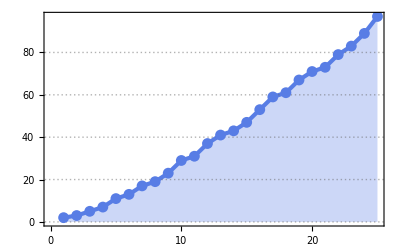

```mathematica
ListLinePlot[Prime[Range[1,25]],PlotTheme->"Business",Filling-> Automatic, Mesh->All]
```

```mathematica
N[1234/5678]   (*approximate an exact quantity*)
```

0.21733

```mathematica
∫_0^1 Sin[x]ⅆx
```

1-Cos[1]

```mathematica
N[%]  (*% shorthand for the last output*)
```

0.459698

```mathematica
∫_0^1 Sin[x]ⅆx //N (* // POSTfix *)
```

## Chapter4 | Word processing and typesetting

## Chapter 5| Presenting with Slide Shows

File -> New -> Slide show

```mathematica
Column[{-Graphics-, "Prediction Plot"}]
```

-Graphics-
Prediction Plot

```mathematica
Column[{-Graphics-, "Prediction Plot"}, Center, 3]  (* 3 determine the verticle spacing between elements *)
```

-Graphics-
Prediction Plot

```mathematica
Grid[{                          (* Grid: 2D layoyt, takes a list of lists; the first sublist becomes the first row*)
{a,b,c},
{d,e,f},
{g, h, i}
}]
```

a | b | c
d | e | f
g | h | i

```mathematica
Grid[{
{"Image",-Graphics-},
{"Color space", "BW"},
{"Dimention", "{1080, 720}"}
}, Alignment->Left, Frame->True, Dividers->All]
```

Image | -Graphics-
Color space | BW
Dimention | {1080, 720}

```mathematica
Style[Grid[{
{Style["Image", Bold, Red],-Graphics-},
{"Color space", "BW"},
{"Dimention", "{1080, 720}"}
}, Alignment->Left, Frame->True, Dividers->All], FontFamily-> "Times"]
```

Image | -Graphics-
Color space | BW
Dimention | {1080, 720}

## Chapter 6| Fundamentals of the Wolfram Language

```mathematica
FullForm[a b + c d]
```

Plus[Times[a,b],Times[c,d]]

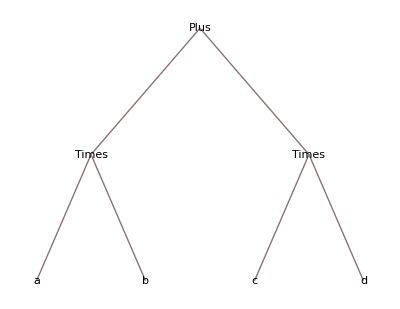

```mathematica
TreeForm[a b+c d]
```

```mathematica
Table[{i, i^2}, {i, 1, 10, 1}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
π Squared is N[π^2]
```

31.0063 is Squared

```mathematica
StringJoin[" The first part ", " and the second part"]
```

The first part  and the second part

```mathematica
ToString[N[π^2]]
```

9.8696

```mathematica
FullForm[%]
```

"9.8696"

```mathematica
StringJoin["π Squared is" , ToString[N[π^2]]]
```

π Squared is9.8696

```mathematica
(10m)/s 5s   (* units *)
```

50 m

```mathematica
Quantity[2, "Feet"] + Quantity[3, "Meters"]
```

1504/127 ft

```mathematica
UnitConvert[%, "Meters"]
```

2256/625 m

```mathematica
Quantity[15,"days"] + Quantity[9,"weeks"]
```

78 days

```mathematica
Today
```

Day: Fri 16 Jun 2023

```mathematica
DatePlus[Today, Quantity[9,"weeks"]]
```

Day: Fri 18 Aug 2023

```mathematica
f[x_]:=x^2 (* Function; left : defintion, right: values *)
```

```mathematica
(* f[x_] function name followed by square brackets
it has to denoted with underscore char _
 := delayed assingment *)
```

```mathematica
Clear[x, f]
```

## Chapter 7| Creating Interactive Models with single command

```mathematica
(* Manipulate[
Expression to manipulate,
Parameter specfication]
*)
```

```mathematica
Manipulate[
Plot[Sin[frequency*x],{x,0,2π}],
{frequency,1,5}]
```

```mathematica
Manipulate[                                                                                   (* Multiple controls *)
Plot[Sin[frequency*x + phase],{x,0,2π}],
{frequency,1,5},{phase, 1, 10}]
```

```mathematica
Manipulate[                                                                                   (* Multiple functions *)
Plot[function[frequency*x + phase],{x,0,2π}],
{frequency,1,5},{phase, 1, 10},{function, {Sin, Cos, Tan, Cot , Csc}, ControlType->RadioButtonBar}]
```

```mathematica
Manipulate[
Expand[(a+b)^n],{n,2,10,1}]
```

```mathematica
Manipulate[
Plot[Sin[f*x],{x,0,2π},PlotLabel->"Sin("<>ToString[f]<>"x)"],  (* String can be joined togther with the <> operator*)
{{f,1,"frequency"},1,5,Appearance->"Labeled"}]
```

## Chapter8| Sharing Mathematica Notebooks

## Chapter 9| Finding Help

```mathematica
?Plot
```

## Chapter 10| 2D and 3D Graphics

WolframAlphaQueryParseResults

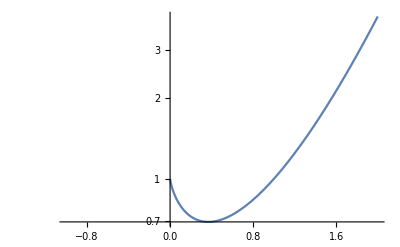

WolframAlphaQueryParseResults

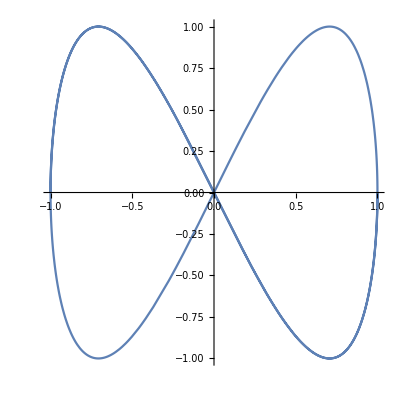

WolframAlphaQueryParseResults

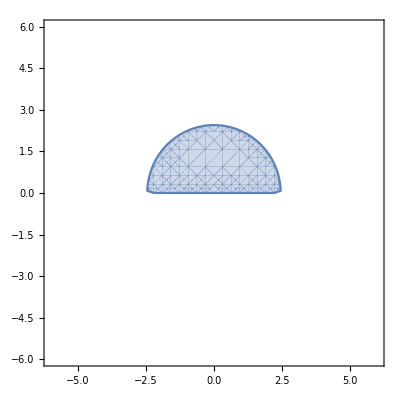

WolframAlphaQueryParseResults

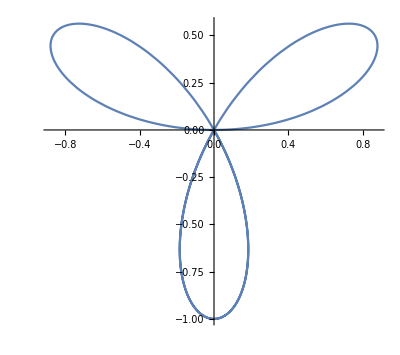

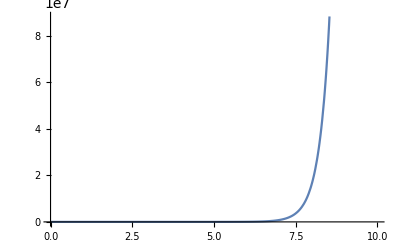

```mathematica
Plot[x^x,{x,0,10}]
```

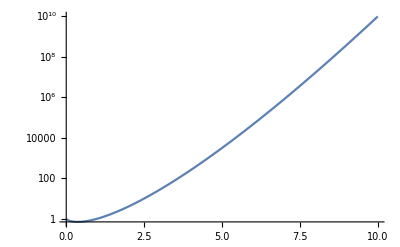

```mathematica
LogPlot[x^x,{x,0,10}]
```

WolframAlphaQueryParseResults (* plotting multiple funs *)

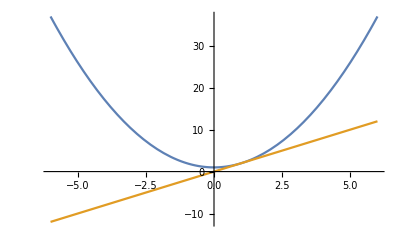

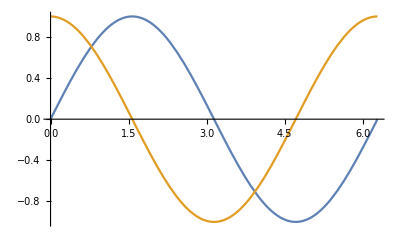

```mathematica
Plot[{Sin[x], Cos[x]}, {x,0,2π}]
```

```mathematica
f[x_]:= x^2+1
```

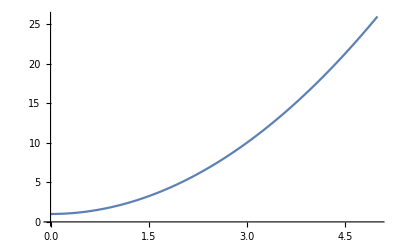

```mathematica
Plot[f[x], {x,0,5}]
```

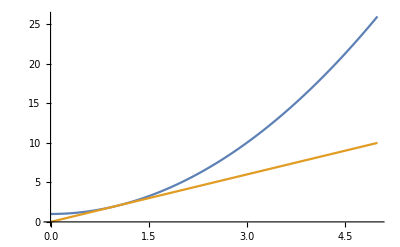

```mathematica
Plot[{f[x], f'[x]}, {x,0,5}]
```

```mathematica
h[x_]:= Piecewise[{{2x, x<0}, {x^2, 0≤x≤2}, {x, x>2}}]
```

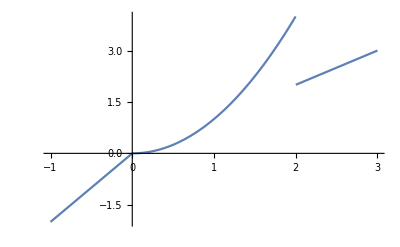

```mathematica
Plot[h[x], {x,-1,3}]
```

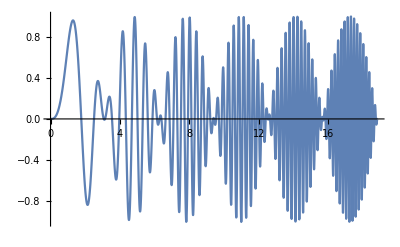

```mathematica
Plot[Sin[x]Sin[x^2],{x, 0, 6π}]
```

```mathematica
Plot3D[Sin[x y],{x,-3,3}, {y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]Cos[y], {x,-3,3},{y,-3,3}, Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]Cos[y], {x,-3,3},{y,-3,3}, Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x y],Cos[y x]}, {x,-3,3},{y,-3,3}, Mesh->None] (* 3D multiple plot *)
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Sin[t]Sin[t^2], {t, 0, π}]
```

-Graphics3D-

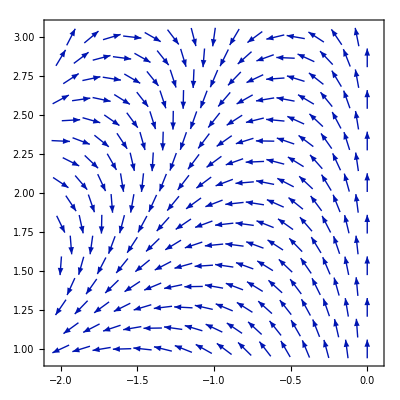

```mathematica
VectorPlot[{Sin[x y ], Cos[x y ]}, {x,-2, 0}, {y, 1,3}]
```

```mathematica
VectorPlot3D[{Sin[x y ], Cos[x y ], Sin[z]}, {x,-2, 0}, {y, 1,3}, {z,0,2}]
```

-Graphics3D-

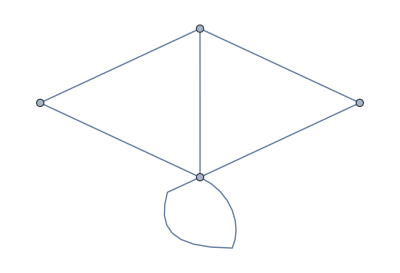

```mathematica
Graph[{1<->2, 2<->3, 3<->1, 2<->4, 1<->4, 2<->2}]  (* ESC ue -> *)
```

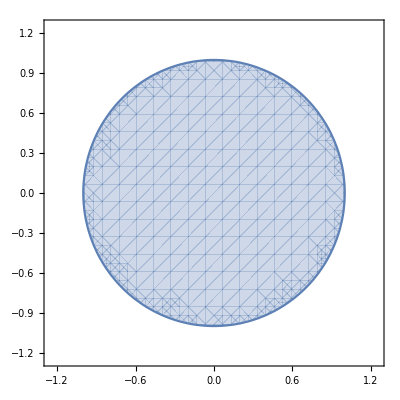

```mathematica
RegionPlot[x^2 +y^2 ≤1, {x, -1.25, 1.25}, {y , -1.25, 1.25}, AxesOrigin->True]
```

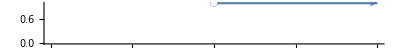

```mathematica
NumberLinePlot[x>1, {x,0,2}]
```

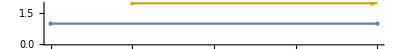

```mathematica
NumberLinePlot[{Interval[{1,5}], Interval[{2,∞ }]}]
```

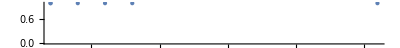

```mathematica
NumberLinePlot[{1,1, 2, 3, 4, 13}]
```

```mathematica
Manipulate[
RegionPlot[x^2+ y^3 <n , {x,-2,2},{y,-2,2}], {n,-1,1}]
```

```mathematica
Clear[x,f,h]
```

## Chapter 11| Visualizing Data

```mathematica
data = {1, 4,9,16,25}
```

{1,4,9,16,25}

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
Manipulate[
lplot[data],
{lplot, {ListPlot, ListLogPlot, ListLogLogPlot}},
Initialization:>(data={1,4, 9, 16, 25})
]
```

```mathematica
ds1 = {1,4,9, 16,25};
```

```mathematica
ds2 = {2,5,7,8};
```

```mathematica
ds3 = {2,5,78,34};
```

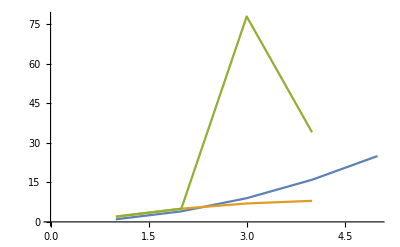

```mathematica
ListLinePlot[{ds1,ds2,ds3}]
```

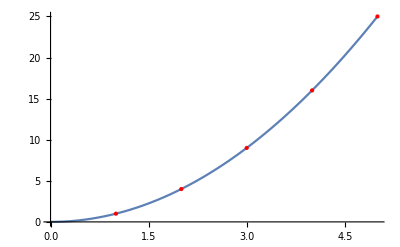

```mathematica
Show[ Plot[x^2, {x,0,5}], ListPlot[{1,4,9,16,25}, PlotStyle->{Red, PointSize[Medium]}]]
```

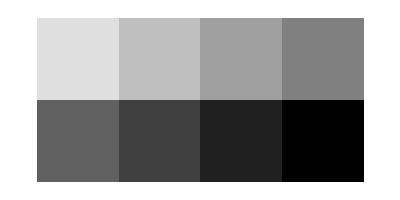

```mathematica
ArrayPlot[{{1,2,3,4}, {5,6,7,8}}]
```

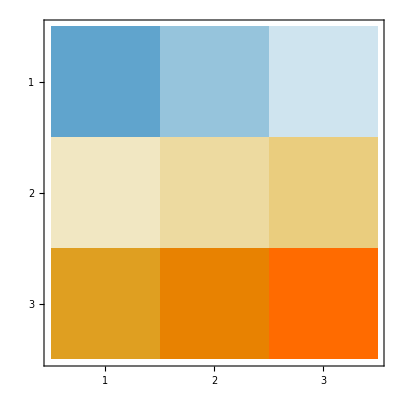

```mathematica
MatrixPlot[{{-10,-5,-1},{2,4,6},{20,30,40}}]
```

```mathematica
d = RandomInteger[{-100,100},{25,25}];
```

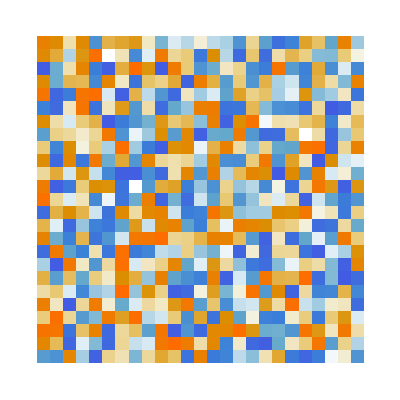
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[d,Frame->False],MatrixPlot[d, Frame->False]}
```

```mathematica
GeoGraphics[Point[GeoPosition[{37.2969,-121,819}]]]
```

-Graphics-

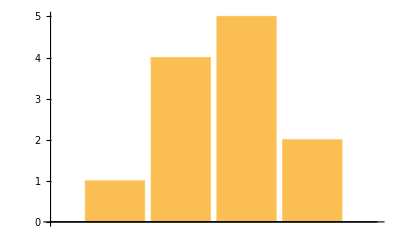

```mathematica
BarChart[{1,4,5,2}]
```

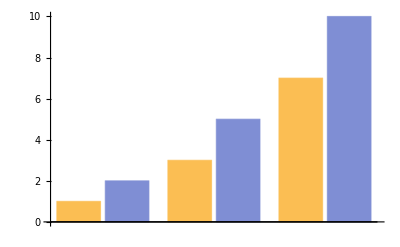

```mathematica
BarChart[{{1,2}, {3,5}, {7,10}}]
```

```mathematica
Manipulate[
function[{{1,2},{3,4},{5,6},{7,8}}],
{function, {PieChart,PieChart3D, SectorChart, BarChart,BarChart3D}}]
```

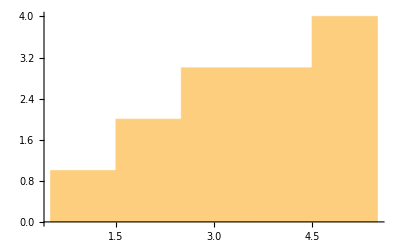

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,5,5,5,5}]
```

```mathematica
WordCloud[{J, A,N,A, R,S}]
```

-Graphics-

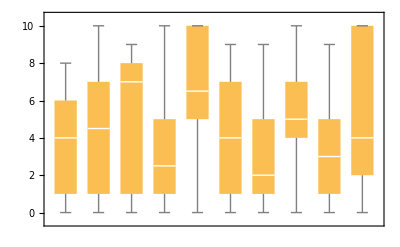

```mathematica
BoxWhiskerChart[RandomInteger[{0,10},{10,10}]]
```

## Chapter 12| Styling and Customizing Graphs

```mathematica
Plot[Sin[x],{x,0,2π}]
```

-Graphics-

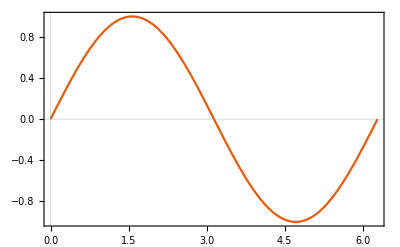

```mathematica
Plot[Sin[x],{x,0,2π}, PlotTheme->"Scientific"]
```

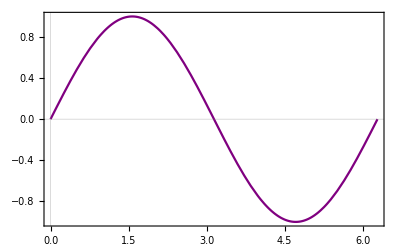

```mathematica
Plot[Sin[x],{x,0,2π}, PlotTheme->"Scientific", PlotStyle->Purple]
```

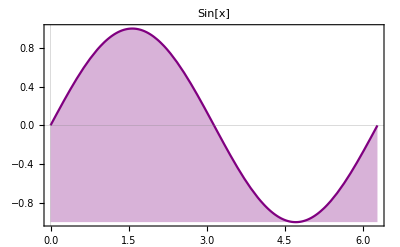

```mathematica
Plot[Sin[x],{x,0,2π}, PlotTheme->"Scientific", PlotStyle->Purple, Filling->Bottom, PlotLabel->"Sin[x]"]
```

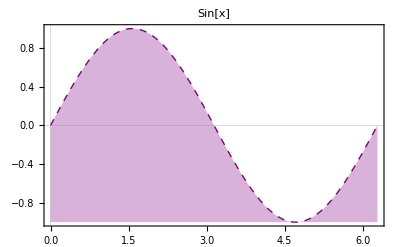

```mathematica
Plot[Sin[x],{x,0,2π}, PlotTheme->"Scientific", PlotStyle->{Purple, Thick, Dashed}, Filling->Bottom, PlotLabel->"Sin[x]"]
```

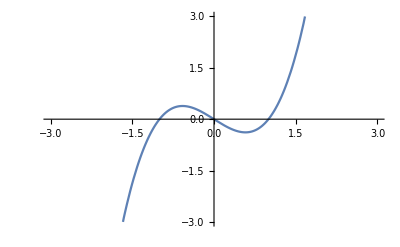

```mathematica
Plot[x^3 - x, {x,-3,3},AxesOrigin->{0,0}, PlotRange->{-3,3}]
```

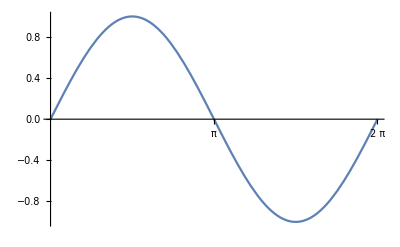

```mathematica
Plot[Sin[x],{x,0,2π}, Ticks->{{π,2π},Automatic}]
```

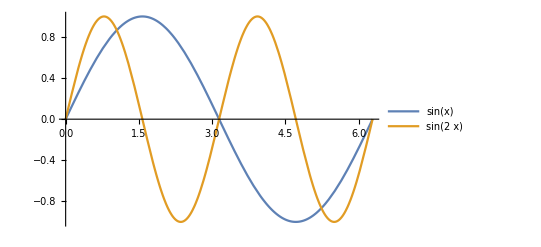

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotLegends-> "Expressions"]
```

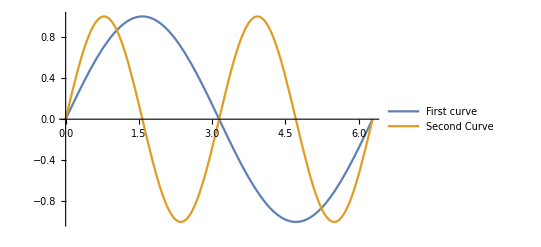

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotLegends->{"First curve", "Second Curve"}]
```

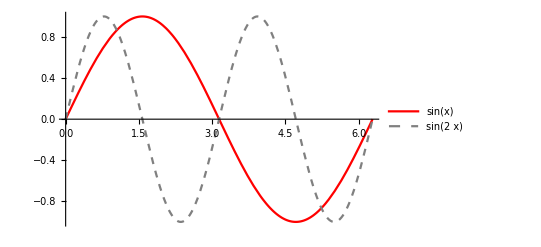

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotStyle-> {Directive[Red, Thick], Directive[Gray,Thick, Dashed]},PlotLegends-> "Expressions"]
```

```mathematica
Plot[Callout[Tan[x],"tan(x)", π],{x,0,2π}]
```

-Graphics-

## Chapter 13| Creating Figures and Diagrams with Graphics Primitives

```mathematica
Disk[]
```

Disk[{0,0}]

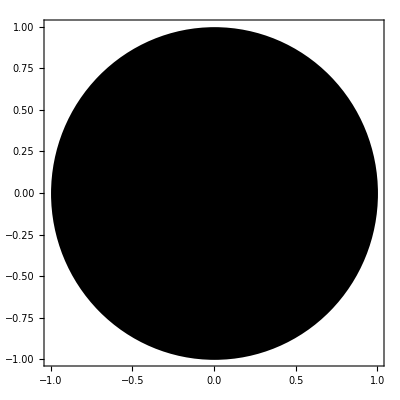

```mathematica
Graphics[Disk[], PlotRange->6, Frame->True]
```

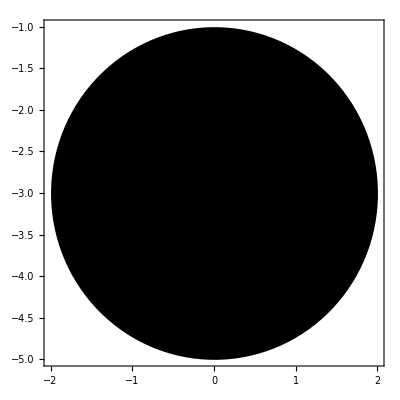

```mathematica
Graphics[Disk[{0,-3},2],PlotRange->6, Frame->True]
```

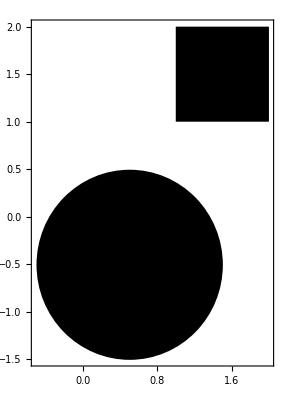

```mathematica
Graphics[{Disk[{0.5,-0.5},1],Rectangle[{1,1},{2,2}]},PlotRange->6, Frame->True]
```

```mathematica
t=2;
```

```mathematica
d = 1/2(-9.8)t^2+50;
```

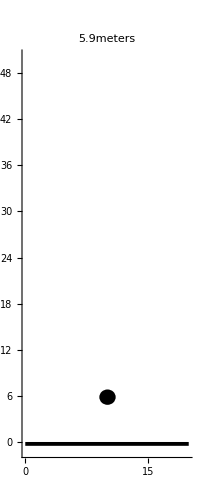

```mathematica
Graphics[{Disk[{10,d}],Rectangle[{0,-0.5},{20,0}]}, PlotRange->{{0,20},{-1,50}},
Axes->{False,True},
PlotLabel->ToString[d]<>"meters"]
```

```mathematica
DynamicModule[{d,t},
Manipulate[Graphics[{Disk[{10,d[t]}],Rectangle[{0,-0.5},{20,0}]}, PlotRange->{{0,20},{-1,50}},
Axes->{False,True},
PlotLabel->ToString[d[t]]<>"meters"],
{t,0,3.2},Initialization:>  (d[t_]:=1/2(-9.8)t^2+50)]]
```

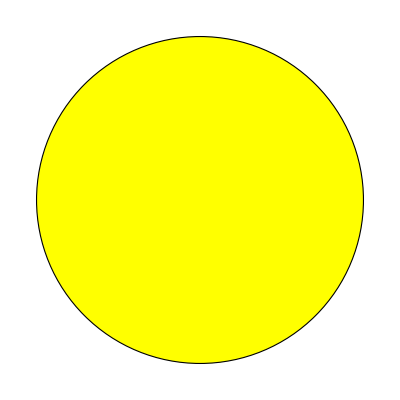

```mathematica
Graphics[{Yellow, EdgeForm[{Black}],Disk[]}]
```

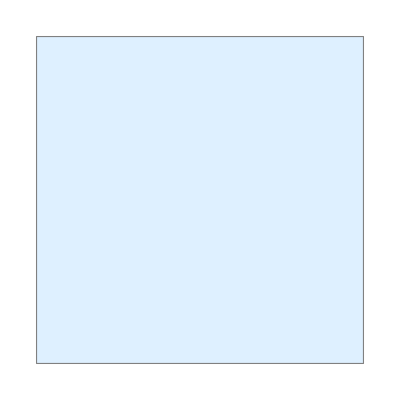

```mathematica
Graphics[{LightBlue, EdgeForm[{Gray, Thick, Dashed}], Rectangle[]}]
```

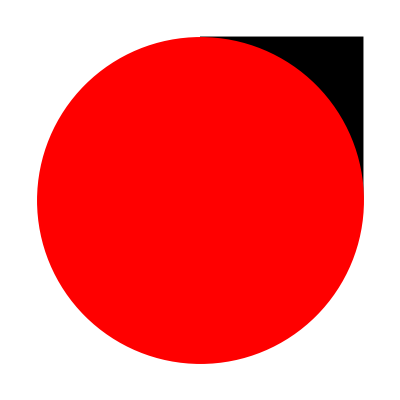

```mathematica
Graphics[{Black, Rectangle[{0,0},{1,1}],Red, Disk[{0,0},1]}]
```

```mathematica
Graphics3D[Sphere[{0,0,0},0.5]]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue, Sphere[{0,0,0},0.5],Green,Sphere[{-0.5,-0.5,-0.5},1]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue,Opacity[0.5], Sphere[{0,0,0},0.5],Green,Sphere[{-0.5,-0.5,-0.5},1]}]
```

-Graphics3D-

## Chapter 14| Algebraic Manipulation and Equation

```mathematica
(2a b)/(b c)
```

(2 a)/c

```mathematica
Expand[(a + b)(a+c)(b+c)]
```

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

```mathematica
Factor[a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2]
```

(a+b) (a+c) (b+c)

```mathematica
Togther[1/(x+1) +1/(x - 1)]
```

Togther[1/(-1+x)+1/(1+x)]

```mathematica
Apart[(2x)/((-1 +x)(1+x))]
```

1/(-1+x)+1/(1+x)

```mathematica
Collect[ax^2+ bx^2 y +c y x, y]
```

ax^2+(bx^2+c x) y

```mathematica
Simplify[Sin[x]^2 + Cos[x]^2]
```

1

```mathematica
Simplify[√(x^2), x>0]
```

x

```mathematica
Solve[x^2+ 2x-1 ==0,x]
```

{{x→-1-√2},{x→-1+√2}}

```mathematica
ReplaceAll[{x,x+1,x+2},x-> 2]
```

{2,3,4}

```mathematica
FindRoot[Sin[x^2]-Cos[x],{x,π}]
```

{x→3.29304}

## Chapter 15| Calculus

```mathematica
D[x^2 Sin[x], x]  (* Diffrentation *)
```

x^2 Cos[x]+2 x Sin[x]

```mathematica
D[x^2 Sin[x], {x,3}]
```

6 Cos[x]-x^2 Cos[x]-6 x Sin[x]

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
f[x_]:= x^3 -2 x^2-5x+6
```

```mathematica
f'[x]
```

-5-4 x+3 x^2

```mathematica
f''[x]
```

```mathematica
-4+6 x
```

-4+6 x

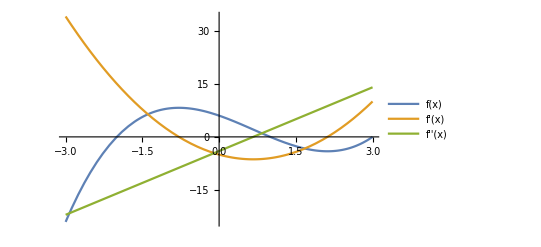

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-3,3}, PlotLegends->"Expressions"]
```

```mathematica
Limit[1/x, x -> 1]
```

1

```mathematica
Limit[1/x, x -> Infinity]
```

0

```mathematica
Integrate[x^2 + 2x+1, x]
```

x+x^2+x^3/3

```mathematica
∫(x^2 + 2x+1)ⅆx
```

x+x^2+x^3/3

```mathematica
Manipulate[
Integrate[x^2 ⅇ^x, {x,0,a}],
{a,0,8}]
```

```mathematica
Clear[x, f]
```

## Chapter 16| Differential Equations

```mathematica
DSolve[y'[x] == x^2 Sin[x], y[x], x]
```

{{y[x]→C[1]-(-2+x^2) Cos[x]+2 x Sin[x]}}

```mathematica
DSolve[{y'[x] == x^2 Sin[x], y[1]==1}, y[x], x]
```

{{y[x]→1-Cos[1]+2 Cos[x]-x^2 Cos[x]-2 Sin[1]+2 x Sin[x]}}

```mathematica
NDSolve[{y'[x]==x^2 Sin[x], y[1]==1}, y,{x,0,10}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
nSlon = NDSolveValue[{y'[x]==x^2 Sin[x], y[1]==1}, y,{x,0,10}]
```

InterpolatingFunction[…]

```mathematica
nSlon[5]
```

-17.3367

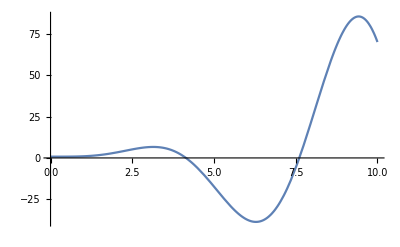

```mathematica
Plot[nSlon[X],{X,0,10}]
```

```mathematica
Clear[nSlon]
```

## Chapter 17 | Linear Algebra

```mathematica
vec1  = {1,2,3,4,57,9,34,8,9,0}  (* vectors*)
```

```mathematica
{1,2,3,4,57,9,34,8,9,0}mjnn
```

```mathematica
vec2 = Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
myFunction[x_]:=x Sin[x]
```

```mathematica
vec3 = Array[myFunction,5]
```

{Sin[1],2 Sin[2],3 Sin[3],4 Sin[4],5 Sin[5]}

```mathematica
vec4 = {a,c,π,ⅇ, 1,2,3,4.5}
```

{a,c,π,ⅇ,1,2,3,4.5}

```mathematica
{VectorQ[vec1],VectorQ[vec2],VectorQ[vec3],VectorQ[vec4]}
```

{True,True,True,True}

```mathematica
vec1 + vec2
```

{2,6,12,20,82,45,83,72,90,100}

```mathematica
Cross[{1,3,5},{π,ⅇ,0}]
```

{-5 ⅇ,5 π,ⅇ-3 π}

```mathematica
Norm[vec3]
```

√(Sin[1]^2+4 Sin[2]^2+9 Sin[3]^2+16 Sin[4]^2+25 Sin[5]^2)

```mathematica
mat1 = {{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
MatrixForm[mat1]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
mat2= Table[i*j,{i,1,5},{j,1,5}];
```

```mathematica
MatrixForm[mat2]
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

```mathematica
myList={1,2,3,4,5,6,7,8,9,10};
```

```mathematica
Part[myList,5]
```

5

```mathematica
myList⟦5⟧
```

5

```mathematica
Part[myList,1;;5]
```

{1,2,3,4,5}

```mathematica
Take[myList,{3,6}]
```

{3,4,5,6}

```mathematica
Take[({{1, 2}, {4, 5}}),2]
```

{{1,2},{4,5}}

```mathematica
Diagonal[({{1, 2}, {4, 6}})]//MatrixForm
```

(1
6)

```mathematica
Transpose[({{1, 2}, {4, 6}})]//MatrixForm
```

(1 | 4
2 | 6)

```mathematica
Inverse[({{1, 2}, {4, 6}})]
```

{{-3,1},{2,-1/2}}

```mathematica
Eigenvalues[({{1, 2}, {4, 6}})]
```

{1/2 (7+√57),1/2 (7-√57)}

## Chapter 18| Probabiity and Statics

WolframAlphaQueryResults

| number of possible hands | approximate probability | approximate chance
5-card hand | 3744 | 0.001441 |  ≈  1 in 694
7-card hand | 3473184 | 0.02596 |  ≈  1 in 39(assuming random selection from a standard 52-card deck)
(the value of a 7-card hand is determined by its best 5-card subset)

WolframAlphaQueryResults

-Graphics-
(assuming fair 6-sided dice)

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/6

```mathematica
probs= Table[
Probability[x+y==12,x\[Distributed]DiscreteUniformDistribution[{1,6}]&&
y\[Distributed]DiscreteUniformDistribution[{1,6}]],
{result,2,12,1}]
```

{1/36,1/36,1/36,1/36,1/36,1/36,1/36,1/36,1/36,1/36,1/36}

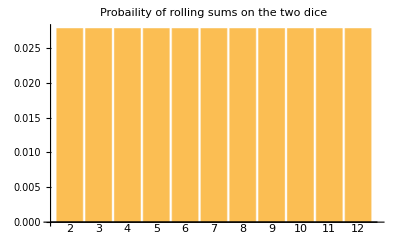

```mathematica
BarChart[probs,ChartLabels->Table[i,{i,2,12,1}],
PlotLabel->"Probaility of rolling sums on the two dice"]
```

```mathematica
PDF[DiscreteUniformDistribution[{1,6}],x]
```

Piecewise[{{1/6, 1≤x≤6}, {0, True}}]

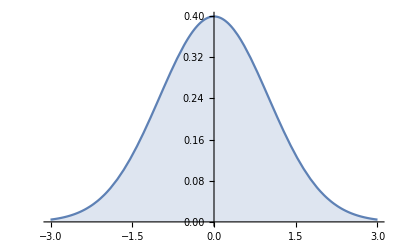

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},Filling->Axis]
```

```mathematica
myFun[x_]:=PDF[NormalDistribution[0,1],x]
```

```mathematica
myFun[0]
```

1/(√(2 π))

```mathematica
points=Table[{x,myFun[x]},{x,-3,3,1}];
```

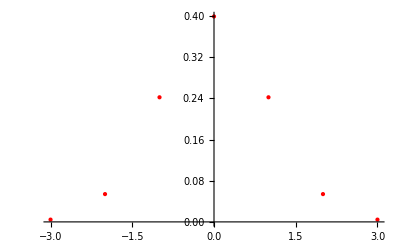

```mathematica
ListPlot[points, PlotStyle->{Red,PointSize[Medium]}]
```

```mathematica
data = {1,2,2,3,4,5,6,6,7,8,8,8,7}
Mean[data]
```

{1,2,2,3,4,5,6,6,7,8,8,8,7}

67/13

```mathematica
Median[data]
```

6

```mathematica
Commonest[data]
```

{8}

```mathematica
Mean[{p1,p2,p3}]
```

1/3 (p1+p2+p3)

```mathematica
Variance[data]
```

82/13

```mathematica
StandardDeviation[data]
```

√(82/13)

```mathematica
InterquartileRange[data]
```

9/2

```mathematica
list1={1,2,2,3,3,4,5,5,5,7};
list2={1,3,4,5,6,7,8,9,0,1};
```

```mathematica
Covariance[list1,list2]
```

26/45

```mathematica
Correlation[list1,list2]
```

2 √(13/5117)

```mathematica
myData=CountryData["Iceland",{{"GDP"},{1970,2010}}]
```

TimeSeries[…]

```mathematica
myData["Values"]
```

QuantityArray[…]

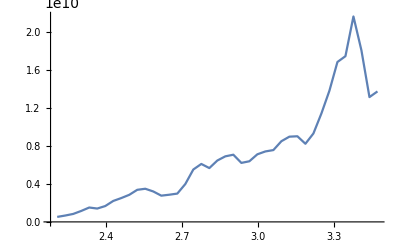

```mathematica
ListLinePlot[myData]
```

```mathematica
data={1,2,3,4,5};
```

```mathematica
GraphicsGrid[{
{BarChart[data],BarChart3D[data]},
{PieChart[data],PieChart3D[data]}
}]
```

-Graphics-

```mathematica
boxData=RandomInteger[{0,4},{4,5}];
```

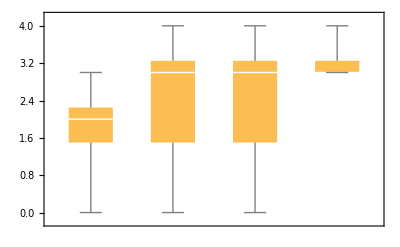

```mathematica
BoxWhiskerChart[boxData]
```

## Chapter 19| Importing and Exporting Data

```mathematica
(* Import[] *)
```

```mathematica
Plot[Sin[x],{x,-2π,2π}]
```

-Graphics-

```mathematica
Export["data.png",Plot[Sin[x],{x,-2π,2π}]]
```

data.png

## Chapter 20| Filtering and Manipulation

```mathematica
Part[{1,2,3,45,67,8},4]
```

45

```mathematica
{1,3,56,78,90,88}[[3]]
```

56

```mathematica
listOfScores = Import["http://www.handsonstart.com/ExampleDataScores.txt","Data"]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
listOfScores⟦1⟧
```

{Joe,Smith,94}

```mathematica
listOfScores⟦1,3⟧
```

94

```mathematica
TableForm[listOfScores]
```

Joe | Smith | 94
Jane | Smith | 85
Bob | Example | 82
Bill | Student | 83
Michelle | Abacus | 98

```mathematica
listOfScores⟦3,All⟧
```

{Bob,Example,82}

```mathematica
listOfScores⟦All,3⟧
```

{94,85,82,83,98}

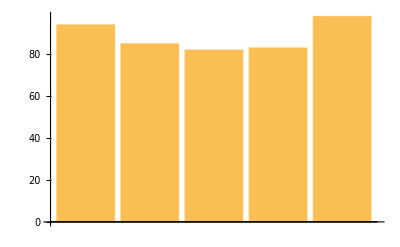

```mathematica
BarChart[listOfScores⟦All,3⟧]
```

```mathematica
newScore=
```

```mathematica
{listOfScores,{"Jana","Anas",95}}
```

{{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}},{Jana,Anas,95}}

## Chapter 21| Working with Curated Data

WolframAlphaQueryParseResults

38019178 people

```mathematica
CountryData["Canada","Airports"]
```

1467

## Chapter 22| Using Wolfram Alpha Data in Mathematica

```mathematica
WolframAlpha["Caffiene"]
```

WolframAlphaQueryResults

## Chapter 23| Statistical Functionality for Data Analysis

## Chapter 24| Creating Programs

```mathematica
Do[Print[x],{x,1,5}]
```

1

2

3

4

5

```mathematica
For [i=1,i≤ 5, i++,Print[i]]
```

1

2

3

4

5

```mathematica
If[π> 3, "My test succeeded"," My test failed!"]
```

My test succeeded

```mathematica
Which[π>5, "Greater than 5", π >3, " Greater than 3", π>1, " Greater than 1"]
```

Greater than 3

## Chapter 25| Creating Parallel and GPU Programs